0

0

1/8 (3+Cos[2 δ])

0

0

0

«1 more identical outputs»

1/4 (3+Cos[2 δ])

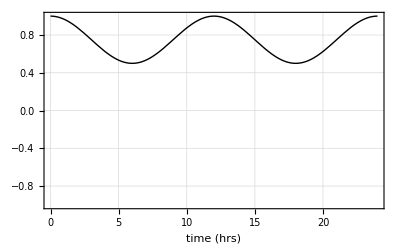

```mathematica
(* pure rotation *)

(* detector locations *)
x1={0,0,0};
x2={0,0,0};

(* unit vectors along the IFO arms *)
(* both arms in rotational plane *)
(*
u1 = {1, 0, 0};
v1 = {0,1,0};
u2={ Cos[δ],Sin[δ], 0};
v2={ -Sin[δ],Cos[δ], 0};
*)

(* one arm in rotational plane *)
u1 = {0, 1, 0};
v1 = {0,0,1};
u2={ -Sin[δ],Cos[δ], 0};
v2={ 0,0, 1};

(* detector tensors *)
d1 = (Outer[Times,u1,u1] - Outer[Times,v1,v1])/2;
d2 = (Outer[Times,u2,u2] - Outer[Times,v2,v2])/2;

(* separation vector *)
(*s = FullSimplify[(x1-x2)/Norm[x1 - x2],{0≤δ≤2Pi}]; *) 
s = {0,0,0};
d = Norm[x1-x2];

(* overlap expression *)
FullSimplify[Tr[d1],{0≤δ≤ 2Pi}]
FullSimplify[Tr[d2],{0≤δ≤ 2Pi}]
FullSimplify[Tr[d1.d2],{0≤δ≤ 2Pi}]
FullSimplify[s.d1.s,{0≤δ≤ 2Pi}]
FullSimplify[s.d2.s,{0≤δ≤ 2Pi}]
FullSimplify[s.(d1.d2).s,{0≤δ≤ 2Pi}]
FullSimplify[(s.d1.s)(s.d2.s),{0≤δ≤ 2Pi}]

M=1/(2 α^2)({{-5 α^2, 10α, 5}, {5 α^2, -10α, 5}, {5 α^2, -10α, -25}, {-5 α^2, 20α, -25}, {5 α^2, -50α, 175}}).{SphericalBesselJ[0,α],SphericalBesselJ[1,α],SphericalBesselJ[2,α]};
γ1=Simplify[Simplify[M[[1]]Tr[d1] Tr[d2]+2M[[2]] Tr[d1.d2]+M[[3]](Tr[d2]s.d1.s+Tr[d1]s.d2.s)+4M[[4]] s.(d1.d2).s+M[[5]](s.d1.s)(s.d2.s)]];

(* make plot *)
 γ1 = Limit[γ1, α->0]
vars1={δ->ω t, ω-> 2 Pi/24};
p1=Plot[{γ1//.vars1},{t,0,24},PlotStyle->{Black,Thick},BaseStyle->{FontSize->16},Frame->True,FrameLabel->{"time (hrs)"},PlotRange->{{0,24},{-1,1}},GridLines->Automatic]
Export["pure_rotation.eps",p1];
```

2 R Sin[δ/2]

0

0

1/2

1/4 (1+Cos[δ])

1/4 (1+Cos[δ])

1/8 (1+Cos[δ])

1/4 Cos[δ/2]^4

1/(64 α^2)5 (2 α^2 (-3+Cos[δ])^2 SphericalBesselJ[0,α]-2 α (15-12 Cos[δ]+5 Cos[2 δ]) SphericalBesselJ[1,α]+(57+60 Cos[δ]+35 Cos[2 δ]) SphericalBesselJ[2,α])

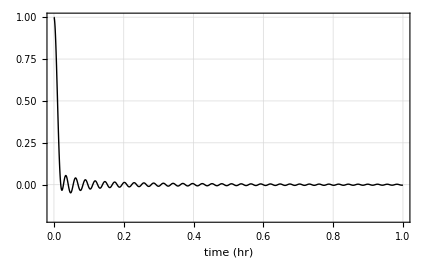

```mathematica
(* pure translation - orbital motion *) 

(* detector locations *)
x1={R,0,0};
x2={R Cos[δ],R Sin[δ], 0};

(* unit vectors along the IFO arms *)
u1 = {0, 1, 0};
v1 = {0,0,1};
u2={ 0,1,0};
v2={ 0,0, 1};

(* detector tensors *)
d1 = (Outer[Times,u1,u1] - Outer[Times,v1,v1])/2;
d2 = (Outer[Times,u2,u2] - Outer[Times,v2,v2])/2;

(* separation vector *)
s = FullSimplify[(x1-x2)/Norm[x1 - x2],{0≤δ≤ 2Pi, R>0}];
d =FullSimplify[ Norm[x1-x2],{0≤δ≤ 2Pi, R>0}]

(* overlap expression *)
FullSimplify[Tr[d1],{0≤δ≤ 2Pi, R>0}]
FullSimplify[Tr[d2],{0≤δ≤ 2Pi, R>0}]
FullSimplify[Tr[d1.d2],{0≤δ≤ 2Pi, R>0}]
FullSimplify[s.d1.s,{0≤δ≤ 2Pi, R>0}]
FullSimplify[s.d2.s,{0≤δ≤ 2Pi, R>0}]
FullSimplify[s.(d1.d2).s,{0≤δ≤ 2Pi, R>0}]
FullSimplify[(s.d1.s)(s.d2.s),{0≤δ≤ 2Pi, R>0}]

M=1/(2 α^2)({{-5 α^2, 10α, 5}, {5 α^2, -10α, 5}, {5 α^2, -10α, -25}, {-5 α^2, 20α, -25}, {5 α^2, -50α, 175}}).{SphericalBesselJ[0,α],SphericalBesselJ[1,α],SphericalBesselJ[2,α]};
γ2=Simplify[Simplify[M[[1]]Tr[d1] Tr[d2]+2M[[2]] Tr[d1.d2]+M[[3]](Tr[d2]s.d1.s+Tr[d1]s.d2.s)+4M[[4]] s.(d1.d2).s+M[[5]](s.d1.s)(s.d2.s)]]

(* make plot *)
vars2={R-> 1.5 10^11,c->3 10^8, f->100, α->2π f d/c, δ->ω t, ω-> 2 Pi/(24 365)};
p2=Plot[{γ2//.vars2},{t,0,1},PlotStyle->{Black,Thick},BaseStyle->{FontSize->16},Frame->True,FrameLabel->{"time (hr)"},PlotRange->{{0,1},{-0.2,1}},GridLines->Automatic]
Export["pure_orbit.eps",p2];
```

2 RE Sin[δ/2]

0

0

1/8 (3+Cos[2 δ])

1/4 (1+Cos[δ])

1/4 (1+Cos[δ])

1/4 Cos[δ/2]^2 Cos[δ]

1/4 Cos[δ/2]^4

1/(64 α^2)5 (2 α^2 (-3+Cos[δ])^2 SphericalBesselJ[0,α]+2 α (-23+12 Cos[δ]+3 Cos[2 δ]) SphericalBesselJ[1,α]+(89+60 Cos[δ]+3 Cos[2 δ]) SphericalBesselJ[2,α])

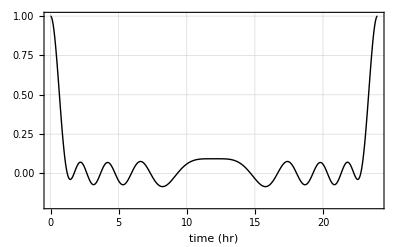

```mathematica
(* rotation of IFOs on surface of earth; no orbital motion *) 

(* detector locations *)
x1={RE,0,0};
x2={RE Cos[δ],RE Sin[δ], 0};

(* unit vectors along the IFO arms *)
u1 = {0, 1, 0};
v1 = {0,0,1};
u2={ -Sin[δ],Cos[δ],0};
v2={ 0,0, 1};

(* detector tensors *)
d1 = (Outer[Times,u1,u1] - Outer[Times,v1,v1])/2;
d2 = (Outer[Times,u2,u2] - Outer[Times,v2,v2])/2;

(* separation vector *)
s = FullSimplify[(x1-x2)/Norm[x1 - x2],{0≤δ≤ 2Pi, RE>0}];
d =FullSimplify[ Norm[x1-x2],{0≤δ≤ 2Pi, RE>0}]

(* overlap expression *)
FullSimplify[Tr[d1],{0≤δ≤ 2Pi, RE>0}]
FullSimplify[Tr[d2],{0≤δ≤ 2Pi, RE>0}]
FullSimplify[Tr[d1.d2],{0≤δ≤ 2Pi, RE>0}]
FullSimplify[s.d1.s,{0≤δ≤ 2Pi, RE>0}]
FullSimplify[s.d2.s,{0≤δ≤ 2Pi, RE>0}]
FullSimplify[s.(d1.d2).s,{0≤δ≤ 2Pi, RE>0}]
FullSimplify[(s.d1.s)(s.d2.s),{0≤δ≤ 2Pi, RE>0}]

M=1/(2 α^2)({{-5 α^2, 10α, 5}, {5 α^2, -10α, 5}, {5 α^2, -10α, -25}, {-5 α^2, 20α, -25}, {5 α^2, -50α, 175}}).{SphericalBesselJ[0,α],SphericalBesselJ[1,α],SphericalBesselJ[2,α]};

γ3=Simplify[Simplify[M[[1]]Tr[d1] Tr[d2]+2M[[2]] Tr[d1.d2]+M[[3]](Tr[d2]s.d1.s+Tr[d1]s.d2.s)+4M[[4]] s.(d1.d2).s+M[[5]](s.d1.s)(s.d2.s)]]

(* make plot *)
vars3={RE-> 6371 10^3,c->3 10^8, f->100, α->2π f d/c ,δ->ω t, ω-> 2 Pi/24};
p3=Plot[{γ3//.vars3},{t,0,24},PlotStyle->{Black,Thick},BaseStyle->{FontSize->16},Frame->True,FrameLabel->{"time (hr)"},PlotRange->{{0,24},{-0.2,1}},GridLines->Automatic]
Export["earth_rotation.eps",p3];
```

√((R+RE-R Cos[β]-RE Cos[δ])^2+(R Sin[β]+RE Sin[δ])^2)

0

0

1/8 (3+Cos[2 δ])

(R Sin[β]+RE Sin[δ])^2/(2 ((R+RE-R Cos[β]-RE Cos[δ])^2+(R Sin[β]+RE Sin[δ])^2))

(R Sin[β-δ]+(R+RE) Sin[δ])^2/(4 (R^2+R RE+RE^2-R (R+RE) Cos[β]+R RE Cos[β-δ]-RE (R+RE) Cos[δ]))

(Cos[δ] (R Sin[β]+RE Sin[δ]) (R Sin[β-δ]+(R+RE) Sin[δ]))/(8 (R^2+R RE+RE^2-R (R+RE) Cos[β]+R RE Cos[β-δ]-RE (R+RE) Cos[δ]))

((R Sin[β]+RE Sin[δ])^2 (R Sin[β-δ]+(R+RE) Sin[δ])^2)/(16 (R^2+R RE+RE^2-R (R+RE) Cos[β]+R RE Cos[β-δ]-RE (R+RE) Cos[δ])^2)

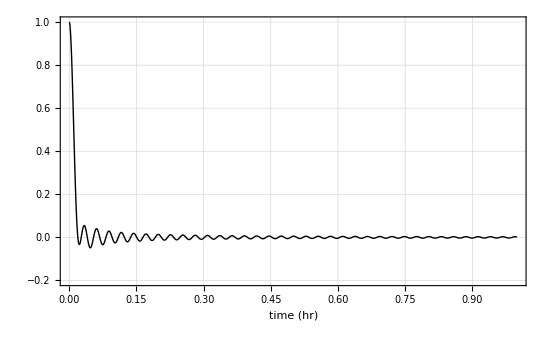

```mathematica
(* rotation of IFOs on surface of earth plus orbital motion *) 

(* position vector of center of earth *)
x01 = {R , 0, 0};
x02 = {R Cos[β], R Sin[β], 0};

(* detector locations *)
x1=x01 +{RE,0,0};
x2=x02+{RE Cos[δ],RE Sin[δ], 0};

(* unit vectors along the IFO arms *)
u1 = {0, 1, 0};
v1 = {0,0,1};
u2={ -Sin[δ],Cos[δ],0};
v2={ 0,0, 1};

(* detector tensors *)
d1 = (Outer[Times,u1,u1] - Outer[Times,v1,v1])/2;
d2 = (Outer[Times,u2,u2] - Outer[Times,v2,v2])/2;

(* separation vector *)
s = FullSimplify[(x1-x2)/Norm[x1 - x2],{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}];
d =FullSimplify[ Norm[x1-x2],{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]

(* overlap expression *)
FullSimplify[Tr[d1],{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[Tr[d2],{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[Tr[d1.d2],{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[s.d1.s,{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[s.d2.s,{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[s.(d1.d2).s,{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]
FullSimplify[(s.d1.s)(s.d2.s),{0≤β≤ 2Pi, 0≤δ≤ 2Pi, R>0, RE>0}]

M=1/(2 α^2)({{-5 α^2, 10α, 5}, {5 α^2, -10α, 5}, {5 α^2, -10α, -25}, {-5 α^2, 20α, -25}, {5 α^2, -50α, 175}}).{SphericalBesselJ[0,α],SphericalBesselJ[1,α],SphericalBesselJ[2,α]};

γ4=Simplify[Simplify[M[[1]]Tr[d1] Tr[d2]+2M[[2]] Tr[d1.d2]+M[[3]](Tr[d2]s.d1.s+Tr[d1]s.d2.s)+4M[[4]] s.(d1.d2).s+M[[5]](s.d1.s)(s.d2.s)]];

(* make plot *)
vars4={R-> 1.5 10^11,RE-> 6371 10^3,c->3 10^8, f->100, α->2π f d/c ,β->ω t, ω-> 2 Pi/(24 365), δ->ωE t, ωE-> 2 Pi/24};
p4=Plot[{γ4//.vars4},{t,0,1},PlotStyle->{Black,Thick}, BaseStyle->{FontSize->16},Frame->True,FrameLabel->{"time (hr)"},PlotRange->{{0,1},{-0.2,1}},GridLines->Automatic]
Export["rotation_and_orbit.eps",p4];
```